```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["data.xlsx"][[1]];
experiment=data[[3;;All,1;;3]];
experiment=Transpose[{Quantity[Around[experiment[[All,1]],0.01],"Millimeters"],Quantity[Around[experiment[[All,2]],0.1],"Milliamperes"],Quantity[Around[experiment[[All,3]],0.1],"Millivolts"]}];
```

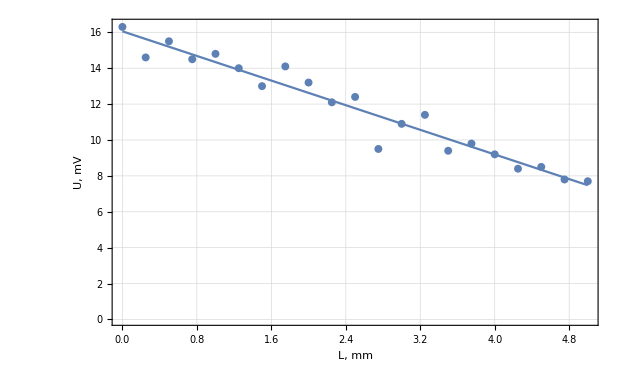

```mathematica
toPlot=Transpose[{experiment[[All,1]],experiment[[All,3]]}];
approx=LinearModelFit[Transpose[{data[[3;;All,1;;3]][[All,1]],data[[3;;All,1;;3]][[All,3]]}],x,x];
Show[ListPlot[Transpose[{experiment[[All,1]],experiment[[All,3]]}],PlotTheme-> "Detailed",FrameLabel->{"L, mm", "U, mV"}],Plot[approx["BestFit"],{x,0,5}]]
```

```mathematica
func[x_]:=Quantity[approx["BestFitParameters"][[1]],"Millivolts"]+Quantity[approx["BestFitParameters"][[2]],"Millivolts"/"Millimeters"]*x;
```

```mathematica
dispersion=toPlot[[All,2]]-func[toPlot[[All,1]]];
```

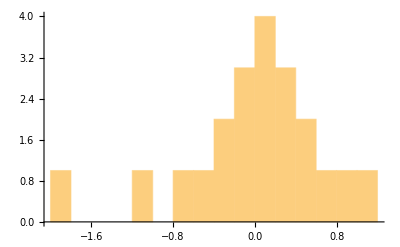

```mathematica
Histogram[dispersion,Length[dispersion]-1]
```

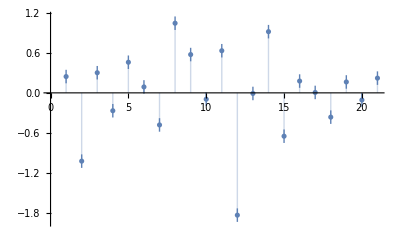

```mathematica
ListPlot[dispersion,Filling->Axis]
```

```mathematica
histData=Transpose[{Table[i,{i,Length[HistogramList[dispersion,10][[2]]]}]/Length[HistogramList[dispersion,10][[2]]],HistogramList[dispersion,10][[2]]}];
```

```mathematica
GaussianModel[x_]=A*Evaluate[PDF[NormalDistribution[μ,σ],x]];
fit=FindFit[histData,GaussianModel[x],{A,μ,σ},x]
```

{A→1.17333,μ→0.689727,σ→0.136311}

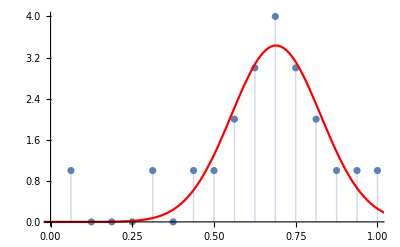

```mathematica
Show[ListPlot[histData,Filling->Axis],Plot[GaussianModel[x]/.fit,{x,-2,2},PlotStyle->Red,PlotRange->Full]]
```